112

Generating graph...

Number of combinations for a 112-coloring of G: 56266306522356343285081647422583851523132412320000000000000000000000000000000000000000

Number of 42-to-112-coloring combinations of G: 0

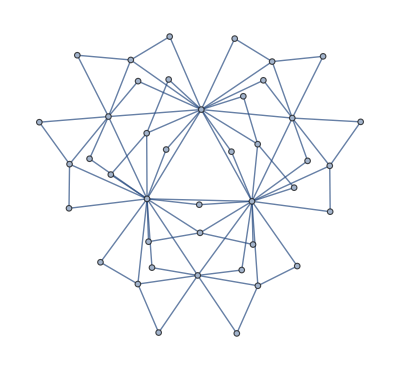

```mathematica
m = <|
	1 -> "Vegetales",
	2 -> "Frutas",
	3 -> "Hortalizas",
	4 -> "Cereales"
|>;
costm = <|
1->11.7,2->12.2,3->14,4->14.5,5->14.7,6->15.0,7->21.1,8->23.1,9->43.1,10->43.2
|>;

k = 112(*Length[m];*)

(*Creation of problem graph*)
(*Ensure g is fully-connected. Can stall if v and e are improper*)
(* Abort execution with CMD+. *)
Print["Generating graph..."]
(*
TimeConstrained[Until[ConnectedGraphQ[g], g = RandomGraph[{vertices, edges}];], 30, Print["Graph generation is stalling. Try to increase E"]];
*)
g = GraphData["DesarguesGraph"];
g = PetersenGraph[5,2];
g = ResourceFunction["DorogovtsevGoltsevMendesGraph"][4];

cp = ChromaticPolynomial[g][k];
Print["Number of combinations for a ", k, "-coloring of G: ", cp];
combinations = 0;
For[i=VertexCount[g], i>=k, i=i-1,
	combinations = ChromaticPolynomial[g][i] + combinations
];
Print["Number of ", VertexCount[g], "-to-", k, "-coloring combinations of G: ", combinations];
g
```

Generating all 3-coloring combinations...

Number of All-3-colorings of G: 6; Took 4.70735s

Best solution: coloring {Frutas,Vegetales,Vegetales,Hortalizas,Vegetales,Vegetales,Vegetales,Hortalizas,Frutas,Hortalizas,Hortalizas,Hortalizas,Hortalizas,Frutas,Hortalizas,Frutas,Frutas,Hortalizas,Vegetales,Vegetales,Frutas,Hortalizas,Frutas,Frutas,Vegetales,Vegetales,Frutas,Vegetales,Hortalizas,Frutas,Frutas,Hortalizas,Frutas,Hortalizas,Hortalizas,Frutas,Vegetales,Vegetales,Frutas,Vegetales,Vegetales,Hortalizas}, with cost 530.6

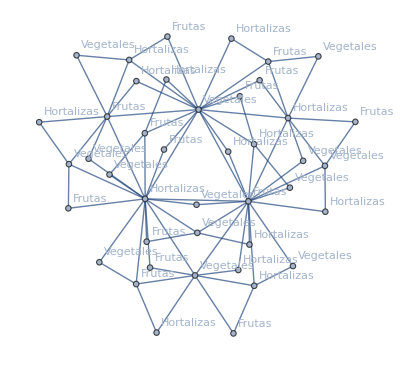

```mathematica
(*Creation of 'individuals'; possible solutions*)
k = 3;
Print["Generating all ", k, "-coloring combinations..."];
{time, vertexColorings} = Timing[ResourceFunction["FindProperColorings" ][g, k]];
FullKColoring[l_List] := CountDistinct[l] == k;
onlyFullKColorings = Select[FullKColoring][vertexColorings];

Print["Number of All-", k, "-colorings of G: ", Length[onlyFullKColorings], "; Took ", time, "s"];


costOfColoring[c_List] :=Plus@@(costm /@ c);
coloringCosts = costOfColoring/@onlyFullKColorings;

(*Ordering[x, 1] gives a max, and Ordering[x, -1] gives a min*)
bestSolution = Ordering[coloringCosts, -1][[1]];
Print["Best solution: coloring ", m/@onlyFullKColorings[[bestSolution]], ", with cost ", coloringCosts[[bestSolution]]];


showVertexColoring[g_Graph, c_List]:=Graph[
g,
VertexLabels->Thread[VertexList[g]->c]
];
(*Show one of the combinations*)
showVertexColoring[g, m/@onlyFullKColorings[[bestSolution]]]
```